```mathematica
Par[x_,y_]:=(x y)/(x+y);
Factor[1/(ⅈ ω C0)+Rs+ⅈ ω Ls]
Factor[Par[1/(ⅈ ω C0)+Rs+ⅈ ω Ls,Rp]]
```

1/ω(3.×10^-10+0. ⅈ) ((3.33333×10^7+1.79505×10^8 ⅈ)+(0.+1. ⅈ) ω) ((-1.79505×10^8-3.33333×10^7 ⅈ)+1. ω)

(1.×10^7 ((-1.79505×10^8-3.33333×10^7 ⅈ)+1. ω) ((1.79505×10^8-3.33333×10^7 ⅈ)+1. ω))/(((0.-1. ⅈ)+1. ω) ((0.-3.33333×10^16 ⅈ)+1. ω))

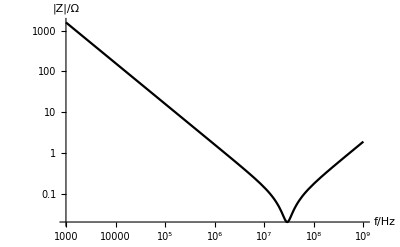

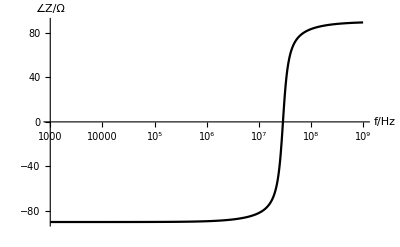

```mathematica
C0=10^-7;Rs=0.02;Ls=300×10^-12;Rp=10^7;
Z[ω_]:=Par[1/(ⅈ ω C0)+Rs+ⅈ ω Ls,Rp];
LogLogPlot[Abs[Z[2 π f]],{f,10^3,10^9},PlotRange->All,PlotTheme->"Monochrome",AxesLabel->{"f/Hz","|Z|/Ω"}]
LogLinearPlot[Arg[Z[2 π f]]*180/π,{f,10^3,10^9},PlotRange->All,PlotTheme->"Monochrome",AxesLabel->{"f/Hz","∠Z/Ω"}]
```